```mathematica
(*Name:Tommy Lee Truong
Last Edit: Dec 9 2016
Program Name: Assignment 4*)
```

Ideal gas law formula P=nRT/V

```mathematica
P[V_,n_,T_]:=(n*.082057338*T)/V
```

Work Formula W=PV

```mathematica
W[p_,V_]:=p*V
```

Ideal gas law in terms of V

```mathematica
Px[V_]:=P[V,1.2,300]
```

Substituting pressure for ideal gas law in work formula

```mathematica
Wx[V_]:=Px[V]*V
```

Change in Volume

```mathematica
V[L_]:=22.1-L
```

Substituting volume for change in volume in work formula

```mathematica
Wy[L_]:=Wx[V[L]]
```

Gas pressure of ideal gas at following change in volume

```mathematica
Wy[1]
```

29.5406

```mathematica
Wy[2]
```

29.5406

```mathematica
Wy[5]
```

29.5406

```mathematica
Wy[10]
```

29.5406

Van der Waals equation

```mathematica
Py[V_,n_,T_,a_,b_]:=(P[1,n,T]/(V-n*b))-(n*n*a/V*V)
```

Substituing volume for change in volume for van der waals in terms of a and b

```mathematica
Pz[L_,a_,b_]:= Py[V[L],1.2,300,a,b]
```

gas pressure of argon at following change in volume

```mathematica
PzAr[L_]:=Pz[L,1.337,0.0320]
```

```mathematica
PzAr[1]
```

-0.522697

```mathematica
PzAr[2]
```

-0.452783

```mathematica
PzAr[5]
```

-0.193869

```mathematica
PzAr[10]
```

0.523868

gas pressure of carbondioxide at following change in volume

```mathematica
PzCO2[L_]:=Pz[L,3.610,0.0429]
```

```mathematica
PzCO2[1]
```

-3.79495

```mathematica
PzCO2[2]
```

-3.72494

```mathematica
PzCO2[5]
```

-3.46566

```mathematica
PzCO2[10]
```

-2.74659

gas pressure of chlorine at following change in volume

```mathematica
PzCl[L_]:=Pz[L,6.254,0.0542]
```

```mathematica
PzCl[1]
```

-7.6014

```mathematica
PzCl[2]
```

-7.53131

```mathematica
PzCl[5]
```

-7.27164

```mathematica
PzCl[10]
```

-6.55119

Graph

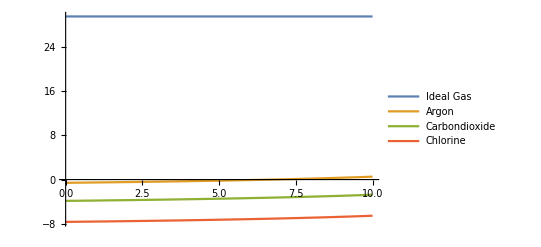

```mathematica
Plot[{Wy[L],PzAr[L],PzCO2[L],PzCl[L]},{L,0,10},PlotLegends->{"Ideal Gas","Argon","Carbondioxide","Chlorine"}]
```